# Sound Speed

## Using Mass Profiles

## Γ = 1 and K = 1

```mathematica
(*This case is somewhat arbitrary. Since the density equation is equal to the pressure equation when Γ and K are equal to 1*)
```

## Γ = 1 and K = r

### Finding dρ/dr

```mathematica
(*We took the mass profile equation for Γ = 1 and K = r. Then made it into the equation for pressure.*)
```

```mathematica
mp2=NDSolveValue[{(-16 π^2 m'[r] ((r^2 (-3+r Λ)+(3+9 r) m[r]) m'[r]+3 r^2 (1+r) m'[r]^2+r^2 (3 r+r^3 Λ-6 m[r]) m''[r]))==0/.{Λ->10^-52},m[0.001]==10^-5,m[9000]==1},m',{r,0.0001,9000}]
```

InterpolatingFunction[…]

```mathematica
(*Below I take the stored mass profile and turn it into a density profile. Then I differentiate the density profile to get dρ/dr for the sound speed equation*)
```

```mathematica
D[mp2[r]/(4 π r^2),r]
```

-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r]

### Finding dp/dr

```mathematica
(*We took the density profile from the last subsection and put it into our EOS with our assumed values to find dp/dr*)
```

```mathematica
D[(mp2[r]/(4 π r^2))r,r]
```

-1/(4 π r^2)InterpolatingFunction[…][r]+1/(4 π r)InterpolatingFunction[…][r]

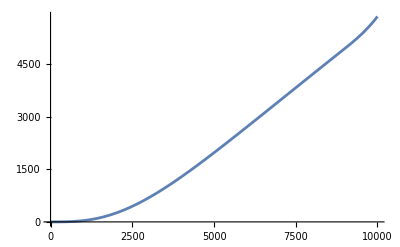

```mathematica
Plot[(-1/(4 π r^2)InterpolatingFunction[…][r]+1/(4 π r)InterpolatingFunction[…][r])/(1/(2 π r^3)InterpolatingFunction[…][r]-1/(4 π r^2)InterpolatingFunction[…][r]),{r,0,10000}]
```

## Γ = 1 and K = r/b

```mathematica
(*We took the stored mass profile for the assumed values for Γ and K from the MassGammaKPlots notebook*)
```

```mathematica
mp3=NDSolveValue[{-1/b^2 16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52,b->10000},m[0.001]==0,m[9000]==1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

### Finding dρ/dr

```mathematica
(*Using the relationship of m'/(4 πr^2)=ρ, we can do a derivative to find dρ/dr*)
```

```mathematica
D[mp3[r]/(4 π r^2),r]
```

-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r]

```mathematica
(*Using the same relationship in the prior section we put our ρ equation into the EOS. Then by differentiating the EOS with respect to r we have dp/dr.*)
```

```mathematica
D[(mp3[r]/(4 π r^2)) r/10000,r]
```

-1/(40000 π r^2)InterpolatingFunction[…][r]+1/(40000 π r)InterpolatingFunction[…][r]

```mathematica
(*Using the chain rule we can take dp/dr and divide it by dρ/dr to find dp/dρ.*)
```

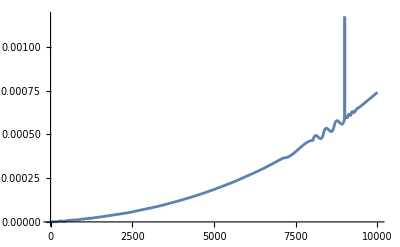

```mathematica
Plot[(-1/(40000 π r^2)InterpolatingFunction[…][r]+1/(40000 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r]),{r,0,10000}]
```

```mathematica
(*Below is taking ρ dp/dρ*)
```

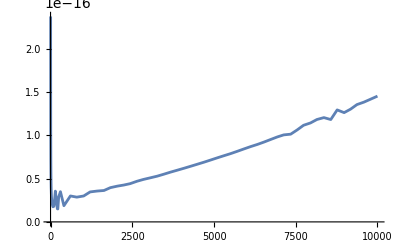

```mathematica
Plot[(mp3[r]/(4 π r^2)) ((-1/(40000 π r^2)InterpolatingFunction[…][r]+1/(40000 π r)InterpolatingFunction[…][r])/(-1/(2 π r^3)InterpolatingFunction[…][r]+1/(4 π r^2)InterpolatingFunction[…][r])),{r,0,10000}]
```